```mathematica
f[z_]:=Exp[Integrate[(A z^2+B z +C)/(z (1-z^2+2k I z)),z]]
dff[z_]:=(A z^2+B z +C)/(z (1-z^2+2k I z))
ddff[z_]:=(2A z+B)/(z (1-z^2+2k I z))+(A(3+A)z^4+(3B-4k I A+2A B)z^3+(-A+3C-4k I B+B^2+2A C)z^2+(2B C-B-4k I C)z+(C^2-C))/(z^2(1-z^2+2k I z)^2)
```

```mathematica
D[w[z],{z,2}]+(2 dff[z]+ (-7/2 z^2 +6k I z+5/2)/(z (1-z^2+2k I z)))D[w[z],{z,1}]+(ddff[z]+ (-7/2 z^2 +6k I z+5/2)/(z (1-z^2+2k I z)) dff[z]-(z+I K^2/4)/(z(1-z^2+2k I z)) )w[z]==0
```

(-((ⅈ K^2)/4+z)/(z (1+2 ⅈ k z-z^2))+(B+2 A z)/(z (1+2 ⅈ k z-z^2))+((5/2+6 ⅈ k z-(7 z^2)/2) (C+B z+A z^2))/(z^2 (1+2 ⅈ k z-z^2)^2)+(-C+C^2+(-B+2 B C-4 ⅈ C k) z+(-A+B^2+3 C+2 A C-4 ⅈ B k) z^2+(3 B+2 A B-4 ⅈ A k) z^3+A (3+A) z^4)/(z^2 (1+2 ⅈ k z-z^2)^2)) w[z]+((5/2+6 ⅈ k z-(7 z^2)/2)/(z (1+2 ⅈ k z-z^2))+(2 (C+B z+A z^2))/(z (1+2 ⅈ k z-z^2))) w'[z]+w''[z]==0

```mathematica
Solve[PolynomialRemainder[(5/2+6 ⅈ k z-(7 z^2)/2) (C+B z+A z^2)+-C+C^2+(-B+2 B C-4 ⅈ C k) z+(-A+B^2+3 C+2 A C-4 ⅈ B k) z^2+(3 B+2 A B-4 ⅈ A k) z^3+A (3+A) z^4,(1-z^2+2k I z),z]==0, {A,B,C}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{C→1/2 (-1-2 A-2 B z-ⅈ k z-4 ⅈ A k z-√((1+2 A+2 B z+ⅈ k z+4 ⅈ A k z)^2-4 (A+A^2+B^2+ⅈ B k+4 ⅈ A B k-2 A k^2-4 A^2 k^2+B z+2 A B z+3 ⅈ A k z+4 ⅈ A^2 k z+2 ⅈ B^2 k z-2 B k^2 z-8 A B k^2 z-4 ⅈ A k^3 z-8 ⅈ A^2 k^3 z)))},{C→1/2 (-1-2 A-2 B z-ⅈ k z-4 ⅈ A k z+√((1+2 A+2 B z+ⅈ k z+4 ⅈ A k z)^2-4 (A+A^2+B^2+ⅈ B k+4 ⅈ A B k-2 A k^2-4 A^2 k^2+B z+2 A B z+3 ⅈ A k z+4 ⅈ A^2 k z+2 ⅈ B^2 k z-2 B k^2 z-8 A B k^2 z-4 ⅈ A k^3 z-8 ⅈ A^2 k^3 z)))}}

```mathematica
1/2 (-1-2 A-2 B z-ⅈ k z-4 ⅈ A k z-√((1+2 A+2 B z+ⅈ k z+4 ⅈ A k z)^2-4 (A+A^2+B^2+ⅈ B k+4 ⅈ A B k-2 A k^2-4 A^2 k^2+B z+2 A B z+3 ⅈ A k z+4 ⅈ A^2 k z+2 ⅈ B^2 k z-2 B k^2 z-8 A B k^2 z-4 ⅈ A k^3 z-8 ⅈ A^2 k^3 z)))/.{A->(-1/2),B->(1/2)}
```

1/2 (-z+ⅈ k z-√((z-ⅈ k z)^2-4 (-(ⅈ k)/2+k^2 z)))

```mathematica
D[w[z],{z,2}]+ (-9/2z^2+(6k I+1)z+5/2 )/(z(1-z^2+2k I z))D[w[z],{z,1}]+((-2z+(1/2-OverHat[k]^2/4 I))/(z(1-z^2+2k I z))+(1/2z^3-(3/4+ k I)z^2+(k I-1/2)z+3/4)/(z(1-z^2+2k I z)^2))w[z]==0
Inactive[DSolve][%,w,z]
DSolveChangeVariables[%,w,OverHat[z],OverHat[z]==z/(I k+Sqrt[1-k^2])]//FullSimplify
Activate[%]
```

((3/4+(-1/2+ⅈ k) z-(3/4+ⅈ k) z^2+z^3/2)/(z (1+2 ⅈ k z-z^2)^2)+(1/2-2 z-(ⅈ (k̂)^2)/4)/(z (1+2 ⅈ k z-z^2))) w[z]+((5/2+(1+6 ⅈ k) z-(9 z^2)/2) w'[z])/(z (1+2 ⅈ k z-z^2))+w''[z]==0

DSolve[((3/4+(-1/2+ⅈ k) z-(3/4+ⅈ k) z^2+z^3/2)/(z (1+2 ⅈ k z-z^2)^2)+(1/2-2 z-(ⅈ (k̂)^2)/4)/(z (1+2 ⅈ k z-z^2))) w[z]+((5/2+(1+6 ⅈ k) z-(9 z^2)/2) w'[z])/(z (1+2 ⅈ k z-z^2))+w''[z]==0,w,z]

DSolve[1/2 (20 k-20 ⅈ √(1-k^2)+(9 ⅈ+2 (k̂)^2)/(ẑ)-(4 k √(1-k^2))/((-1+ẑ) (1+ẑ (2-4 k^2+ẑ)))-(4 k √(1-k^2) ẑ)/((-1+ẑ) (1+ẑ (2-4 k^2+ẑ)))+(ⅈ (1+ẑ)^2)/(ẑ (1+ẑ (2-4 k^2+ẑ)))) w[ẑ]+(2 (5 (k+ⅈ √(1-k^2))+ẑ (2 ⅈ-12 k+9 (k-ⅈ √(1-k^2)) ẑ)) w'[ẑ])/(ẑ)+4 (-1+ẑ) (-ⅈ √(1-k^2)+k (-1+ẑ)-ⅈ √(1-k^2) ẑ) w''[ẑ]==0,w,ẑ]

Part::partw: Part 2 of {1} does not exist.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Solve::svars: Equations may not give solutions for all "solve" variables.

Part::partw: Part 2 of {1} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

DSolve[1/2 (20 k-20 ⅈ √(1-k^2)+(9 ⅈ+2 (k̂)^2)/(ẑ)-(4 k √(1-k^2))/((-1+ẑ) (1+ẑ (2-4 k^2+ẑ)))-(4 k √(1-k^2) ẑ)/((-1+ẑ) (1+ẑ (2-4 k^2+ẑ)))+(ⅈ (1+ẑ)^2)/(ẑ (1+ẑ (2-4 k^2+ẑ)))) w[ẑ]+(2 (5 (k+ⅈ √(1-k^2))+ẑ (2 ⅈ-12 k+9 (k-ⅈ √(1-k^2)) ẑ)) w'[ẑ])/(ẑ)+4 (-1+ẑ) (-ⅈ √(1-k^2)+k (-1+ẑ)-ⅈ √(1-k^2) ẑ) w''[ẑ]==0,w,ẑ]

```mathematica
D[w[z],{z,2}]+ (-9/2z^2+(6k I+1)z+5/2 )/(z(1-z^2+2k I z))D[w[z],{z,1}]+((-2z+(1/2-OverHat[k]^2/4 I))/(z(1-z^2+2k I z))+(1/2z^3-(3/4+ k I)z^2+(k I-1/2)z+3/4)/(z(1-z^2+2k I z)^2))w[z]==0
Inactive[DSolve][%,w,z]
Activate[%]
```

((3/4+(-1/2+ⅈ k) z-(3/4+ⅈ k) z^2+z^3/2)/(z (1+2 ⅈ k z-z^2)^2)+(1/2-2 z-(ⅈ (k̂)^2)/4)/(z (1+2 ⅈ k z-z^2))) w[z]+((5/2+(1+6 ⅈ k) z-(9 z^2)/2) w'[z])/(z (1+2 ⅈ k z-z^2))+w''[z]==0

DSolve[((3/4+(-1/2+ⅈ k) z-(3/4+ⅈ k) z^2+z^3/2)/(z (1+2 ⅈ k z-z^2)^2)+(1/2-2 z-(ⅈ (k̂)^2)/4)/(z (1+2 ⅈ k z-z^2))) w[z]+((5/2+(1+6 ⅈ k) z-(9 z^2)/2) w'[z])/(z (1+2 ⅈ k z-z^2))+w''[z]==0,w,z]

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 1-2 k^2+k^4 == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{w→}}

```mathematica
PhiFlat[a_]:=(1+a^4)^(1/4)Exp[1/2 I ArcTan[a^2]]HeunG[-1,1/4(5- I K^2),1,5/2,5/2,1/2,a^2 I];
PsiFlat[a_]:=Exp[-I Pi/4](EllipticPi[1/2 I (K^2-Sqrt[K^4-4]),ArcSin[Exp[I Pi /4]*a],-1]-EllipticPi[1/2 I (K^2+Sqrt[K^4-4]),ArcSin[Exp[I Pi /4]*a],-1]);
PhiFlatInt[a_]:=3Sqrt[1+a^2K^2+a^4]/(a^3 K Sqrt[K^4-4])Sin[K Sqrt[K^4-4]PsiFlat[a]];
```

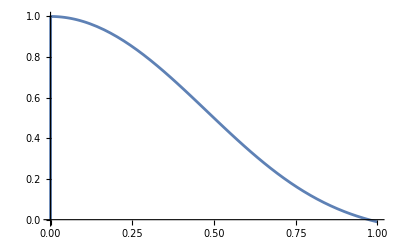

```mathematica
Plot[PhiFlat[a]/.{K->5}, {a,0,1}]
```

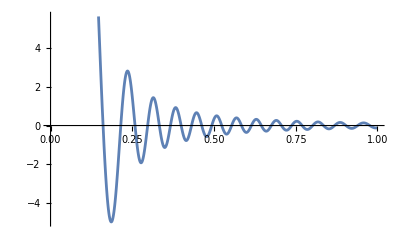

```mathematica
Plot[Re[PhiFlatInt[a]]/.{K->5}, {a,0,1}]
```

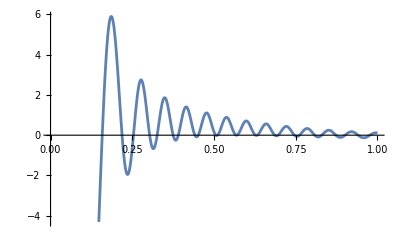

```mathematica
Plot[N[Re[PhiFlat[a]-PhiFlatInt[a]]/.{K->5}], {a,0,1}]
```